```mathematica
filesAR=FileNames["/home/carla/GDC/SED/GDC_Conf_AR_SED_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/SED/GDC_Conf_BR_SED_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]];
confBR=dataBR[[All,1]];
```

```mathematica
dojAR=confAR[[All,1]][[All,1]]
zAR=confAR[[All,2]][[All,1]]
fAR=confAR[[All,3]][[All,1]]
```

{0.00473934,0.00473934,0.00249377,0.00051573,0.00054615,1.}

{0.00460268,0.00460652,0.00246674,0.000512793,0.000543225,1.}

{0.943946,0.945481,0.978558,0.988675,0.989347,1}

```mathematica
dojBR=confBR[[All,1]][[All,1]]
zBR=confBR[[All,2]][[All,1]]
fBR=confBR[[All,3]][[All,1]]
```

{0.00473934,0.00249377,0.00051573,0.00051573,0.00054615}

{0.00460652,0.00246674,0.000512793,0.000512805,0.00054322}

{0.945481,0.978558,0.988675,0.988722,0.98933}

```mathematica
sList={3,4,5,6,7,8};
sList2={3.5,4.5,5.5,6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];


dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran];
zPAR= {#[[2]],#[[1]]}&/@Map[{zAR[[#]],sList[[#]]}&,ran];
fPAR= {#[[2]],#[[1]]}&/@Map[{fAR[[#]],sList[[#]]}&, ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&,ran2];
zPBR= {#[[2]],#[[1]]}&/@Map[{zBR[[#]],sList2[[#]]}&,ran2];
fPBR= {#[[2]],#[[1]]}&/@Map[{fBR[[#]],sList2[[#]]}&, ran2];
```

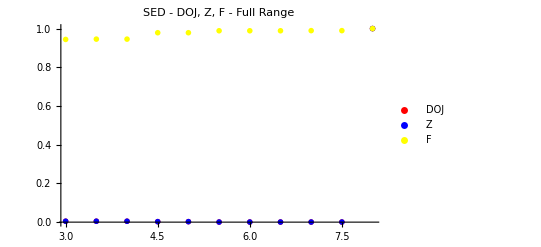

```mathematica
PlotAllParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->All, PlotLabel->"SED - DOJ, Z, F - Full Range", PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
```

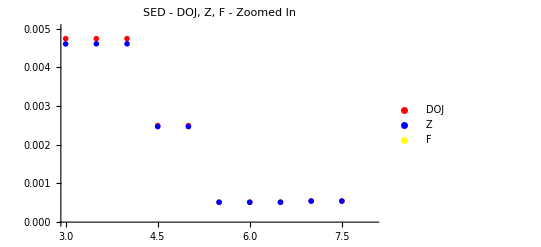

```mathematica
PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{0, 0.005},  PlotLabel->"SED - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/SED/"];
(*Put[{confM,{bvE,bvHEK}},filenameOut]*)
Put[Union[dojPAR,dojPBR],"SED_DOJ.txt"]
Put[Union[zPAR, zPBR],"SED_Z.txt"]
Put[Union[fPAR,fPBR],"SED_F.txt"]
Export["SED_ALL.jpeg",PlotAllParts,ImageSize->850]
Export["SED_Zoomed_In.jpeg",PlotParts,ImageSize->850]
```

SED_ALL.jpeg

SED_Zoomed_In.jpeg